```mathematica
(*Mathematica*)
```

```mathematica
(*1-4-1 vertex octahedron*)
```

```mathematica
p1={{0,0,1.0}}
```

{{0,0,1.}}

```mathematica
p2=N[{{1,1,0},{1,-1,0},{-1,-1,0},{-1,1,0}}/Sqrt[2]]
```

{{0.707107,0.707107,0.},{0.707107,-0.707107,0.},{-0.707107,-0.707107,0.},{-0.707107,0.707107,0.}}

```mathematica
p3={{0,0,-1.0}}
```

{{0,0,-1.}}

```mathematica
pts1=Join[p1,p2,p3]
```

{{0,0,1.},{0.707107,0.707107,0.},{0.707107,-0.707107,0.},{-0.707107,-0.707107,0.},{-0.707107,0.707107,0.},{0,0,-1.}}

```mathematica
p[z_]=ExpandAll[Product[z-(pts1[[i,1]]+I*pts1[[i,2]])/(Sqrt[2]+pts1[[i,3]]),{i,6}]]//Chop
```

0.25 z^2+z^6

```mathematica
g1=ListPointPlot3D[pts1,PlotStyle->Red]
```

-Graphics3D-

```mathematica
R1=ConvexHullRegion[pts1]
```

Polyhedron[…]

```mathematica
g1a=Show[Graphics3D[{Opacity[0.5],Blue,R1}]]
```

-Graphics3D-

```mathematica
g3=Show[{g1,g1a},AspectRatio->1]
```

-Graphics3D-

```mathematica
(*2-2-2 vertex octahedron*)
```

```mathematica
p12={{0,1,1},{0,-1,1}}/Sqrt[2]
```

{{0,1/(√2),1/(√2)},{0,-1/(√2),1/(√2)}}

```mathematica
p22={{1,0,0},{-1,0,0}}
```

{{1,0,0},{-1,0,0}}

```mathematica
p23={{0,1,-1},{0,-1,-1}}/Sqrt[2]
```

{{0,1/(√2),-1/(√2)},{0,-1/(√2),-1/(√2)}}

```mathematica
pts2=Join[p12,p22,p23]
```

{{0,1/(√2),1/(√2)},{0,-1/(√2),1/(√2)},{1,0,0},{-1,0,0},{0,1/(√2),-1/(√2)},{0,-1/(√2),-1/(√2)}}

```mathematica
q[z_]=ExpandAll[Product[z-(pts2[[i,1]]+I*pts2[[i,2]])/(1+pts2[[i,3]]),{i,6}]]//Chop
```

-1/((-1+√2)^2 (1+√2)^2)-z^2/(-1+√2)^2-z^2/(1+√2)^2+z^2/((-1+√2)^2 (1+√2)^2)-z^4+z^4/(-1+√2)^2+z^4/(1+√2)^2+z^6

```mathematica
g2=ListPointPlot3D[pts2,PlotStyle->Blue]
```

-Graphics3D-

```mathematica
R2=ConvexHullRegion[pts2]
```

Polyhedron[…]

```mathematica
g2a=Show[Graphics3D[{Opacity[0.5],Red,R2}]]
```

-Graphics3D-

```mathematica
g4=Show[{g2,g2a},AspectRatio->1]
```

-Graphics3D-

```mathematica
gout=Show[{g3,g4},PlotRange->All,ViewPoint->{2,2,2},AspectRatio->1,ImageSize->2000];
```

```mathematica
Export["octahedrons_Orthogonal.jpg",gout]
```

octahedrons_Orthogonal.jpg

```mathematica
(*renormaklization on 90 degree octahedrons*)
```

```mathematica
ph[x_]=Together[ExpandAll[x^2*p[x]/q[x]]]
```

(1. (0.25 x^4+x^8))/(-1.-5. x^2+5. x^4+x^6)

```mathematica
w=x/.NSolve[ph[x]==0,x]
```

{0.5-0.5 ⅈ,0.5+0.5 ⅈ,-0.5-0.5 ⅈ,-0.5+0.5 ⅈ,0.,0.,0.,0.}

```mathematica
max=Max[Norm/@w]+1
```

1.70711

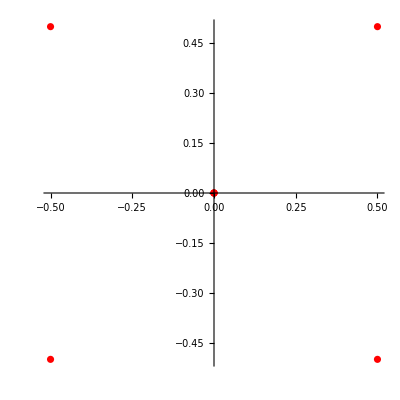

```mathematica
ComplexListPlot[w,PlotStyle->Red,ImageSize->Full]
```

```mathematica
ga=ComplexPlot[ph[z],{z,-max-max*I,max+max*I},ColorFunction->"CyclicReImLogAbs",ImageSize->2000];
```

```mathematica
gb=ComplexPlot3D[ph[z],{z,-max-max*I,max+max*I},ColorFunction->"CyclicReImLogAbs",ImageSize->2000];
```

```mathematica
g1=JuliaSetPlot[ph[z],z,ColorFunction->Hue,ImageSize->2000,AspectRatio->1,ImageResolution->2000,PerformanceGoal->"Quality",Frame->False,Axes->False,PlotRange->All];
```

```mathematica
g2=ListPlot[JuliaSetPoints[ph[z],z],ImageSize->2000,PlotStyle->{PointSize[0.001]},ColorFunction->Hue,PlotRange->All,AspectRatio->1];
```

```mathematica
Export["Julia_Herman_Orthogonal_Octahedrons_grid.jpg",GraphicsGrid[{{ga,gout},{g1,g2}},ImageSize->{4000,4000}]]
```

```mathematica
(*end*)
```